```mathematica
(* Solve[{x^2+y^2==y*sin(t)+x*cos(t),x^2+y^2==-y*sin((3*t)/4)-x*cos((3*t)/4)},{x,y},Reals] *)

(* Solve x *)
Print[FullSimplify[−((cos((3 t)/4) (sin(t))^2+(cos((3 t)/4) sin((3 t)/4)−sin((3 t)/4) cos(t)) sin(t)−(sin((3 t)/4))^2 cos(t))/((sin(t))^2+2 sin((3 t)/4) sin(t)+(cos(t))^2+2 cos((3 t)/4) cos(t)+(sin((3 t)/4))^2+(cos((3 t)/4))^2))]];
Print[TrigExpand[(Cos[t]-Cos[3t/4])/2]];
Print[FullSimplify[4 Cos[t/4]^4-2 Cos[t/4]^3-4 Cos[t/4]^2+3/2 Cos[t/4]+1/2 ]];
```

1/2 (-Cos[(3 t)/4]+Cos[t])

-1/2 Cos[t/4]^3+1/2 Cos[t/4]^4+3/2 Cos[t/4] Sin[t/4]^2-3 Cos[t/4]^2 Sin[t/4]^2+1/2 Sin[t/4]^4

1/2 (-Cos[(3 t)/4]+Cos[t])

```mathematica
(* Solve y *)
Print[FullSimplify[((cos((3 t)/4) cos(t)+(cos((3 t)/4))^2) sin(t)−sin((3 t)/4) (cos(t))^2−cos((3 t)/4) sin((3 t)/4) cos(t))/((sin(t))^2+2 sin((3 t)/4) sin(t)+(cos(t))^2+2 cos((3 t)/4) cos(t)+(sin((3 t)/4))^2+(cos((3 t)/4))^2)]];
Print[TrigExpand[(Sin[t]-Sin[3t/4])/2]];
Print[FullSimplify[4Sin[t/4] Cos[t/4]^3-2Sin[t/4] Cos[t/4]^2-2Sin[t/4]Cos[t/4]+1/2 Sin[t/4] ]];
```

1/2 (-Sin[(3 t)/4]+Sin[t])

-3/2 Cos[t/4]^2 Sin[t/4]+2 Cos[t/4]^3 Sin[t/4]+1/2 Sin[t/4]^3-2 Cos[t/4] Sin[t/4]^3

1/2 (-Sin[(3 t)/4]+Sin[t])

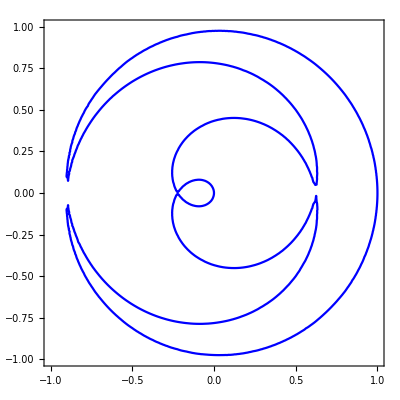

```mathematica
ContourPlot[0==-64*y^8-256*x^2*y^6+112*y^6-384*x^4*y^4+336*x^2*y^4-56*y^4-256*x^6*y^2+336*x^4*y^2-112*x^2*y^2+7*y^2-64*x^8+112*x^6-56*x^4+7*x^2+x,{x,-1,1},{y,-1,1},ContourStyle->Blue]
```